## Finite-size correction of generalized inverse participation ratio (GIPR) --α_q

We have a set of generalized inverse participation ratio (GIPR) α_q, which are numerically computed by cluster computer and stored in a csv file. We want to find the critical disorder strength W_c at which the α_q become independent of system size, i.e. α_q VS W curves for different system sizes crosses at W_c. However due to finite size effect, the crossings are different for different system sizes. This can be corrected by finite size correction. 

From scaling collapse analysis, we know that
				α_q=F(L^(1/ν)(W-W_c))
For finite size, above equation should have the following finite size correction (see Ref. PHYSICAL REVIEW B 83, 184206 (2011))
				α_q=L^d_2(F(L^(1/ν)(W-W_c))+A_0/L^y+A_1/L^(2y)+⋯)
Here we take d_2=0, and consider up to first order correction. Thus we are going to fit 
				Y_L(W) = α_(L,q)(W)-A_0/L^y 
Therefore we have two fitting parameters A_0, y.

### The fitting procedure

For a given set of {A_0,y}, we first polynomially fit Y, i.e we suppose 
				Y(W)=a + b W + c W^2 + d W^3 
then find a,b,c,d that best fits Y. After fitting we compute the crossings of different curves denoted by W_j+δW_j, where j∈[1,N_cross], N_cross is number of crossing point, δW_j is uncertainty in W_j calculated from uncertainties in fitting parameters. For correct set of A_0, y, all curves (Y vs W) cross at W_c. We can find W_c by minimizing 
				χ^2=∑_(j=1)^N_cross ((W_j - W_c)/δW_j)^2
over A_0,y, W_c.

### Computation

The data is stored in “results.dat” file in the same directory with current notebook.

```mathematica
Llist={"100","500","1000","5000","10000"};   (* list of system sizes*)
```

```mathematica
(* setting up the path *)
path2=NotebookDirectory[];
SetDirectory[path2];
```

#### Loading the data

```mathematica
file="results.dat";
data=Import[file];
```

```mathematica
Dimensions[data]
```

{1615,15}

First we fit α_(q=0). So we extract {σ,W, α_(q=0)} for different L.

```mathematica
α1 = Select[data,#[[1]]==100 &][[All,{2,3,4}]];
α2 = Select[data,#[[1]]==500 &][[All,{2,3,4}]];
α3 = Select[data,#[[1]]==1000 &][[All,{2,3,4}]];
α4 = Select[data,#[[1]]==5000 &][[All,{2,3,4}]];
α5 = Select[data,#[[1]]==10000 &][[All,{2,3,4}]];
```

#### Polynomial fit

```mathematica
(* initialize the parameters *)
A0=0.5;
y=1.0;
sig=0.45;
```

The Y functions for σ=0.35

```mathematica
Y1 =MapAt[# &,Select[α1,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y2 =MapAt[#&,Select[α2,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y3 =MapAt[#&,Select[α3,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y4 =MapAt[#&,Select[α4,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y5 =MapAt[#&,Select[α5,#[[1]]==sig &][[All,{2,3}]],{All,2}];
```

```mathematica
(* fit1=FindFit[Y1[[4;;]],a + b x + c x^2 +dd x^3 + e x^4 + f x^5,{a,b,c,dd, e, f},x];
f1[x_]= a +b x + c x^2 + dd x^3 + e x^4 + f x^5/.fit1;
fit2=FindFit[Y2[[4;;]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5,{a,b,c,dd, e, f},x];
f2[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5/.fit2;
fit3=FindFit[Y3[[4;;]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5,{a,b,c,dd, e, f},x];
f3[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5/.fit3;
fit4=FindFit[Y4[[4;;]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5,{a,b,c,dd, e, f},x];
f4[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5/.fit4;
fit5=FindFit[Y5[[4;;]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5,{a,b,c,dd, e, f},x];
f5[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5/.fit5;*)
```

```mathematica
fit1=FindFit[Y1[[4;;12]],a + b x + c x^2 +dd x^3,{a,b,c,dd},x];
f1[x_]= a +b x + c x^2 + dd x^3/.fit1;
fit2=FindFit[Y2[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 ,{a,b,c,dd, e},x];
f2[x_]= a +b x + c x^2 + dd x^3+ e x^4 /.fit2;
fit3=FindFit[Y3[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5,{a,b,c,dd, e,f},x];
f3[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5/.fit3;
fit4=FindFit[Y4[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5+g x^6,{a,b,c,dd, e,f,g,h},x];
f4[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5+g x^6/.fit4;
fit5=FindFit[Y5[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5+g x^6+h x^7,{a,b,c,dd, e,f,g,h,k},x];
f5[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5+g x^6+h x^7/.fit5;
```

Check if the fitting is working

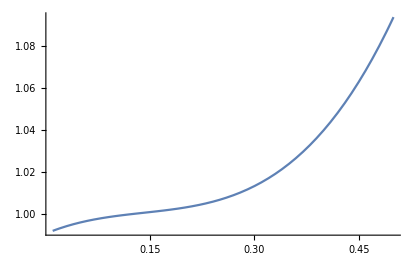

```mathematica
Show[{Plot[{f1[x]},{x,0.01,0.5}],ListLinePlot[Table[f1[i],{i,0.02,0.5,0.02}],PlotMarkers->Automatic]}]
```

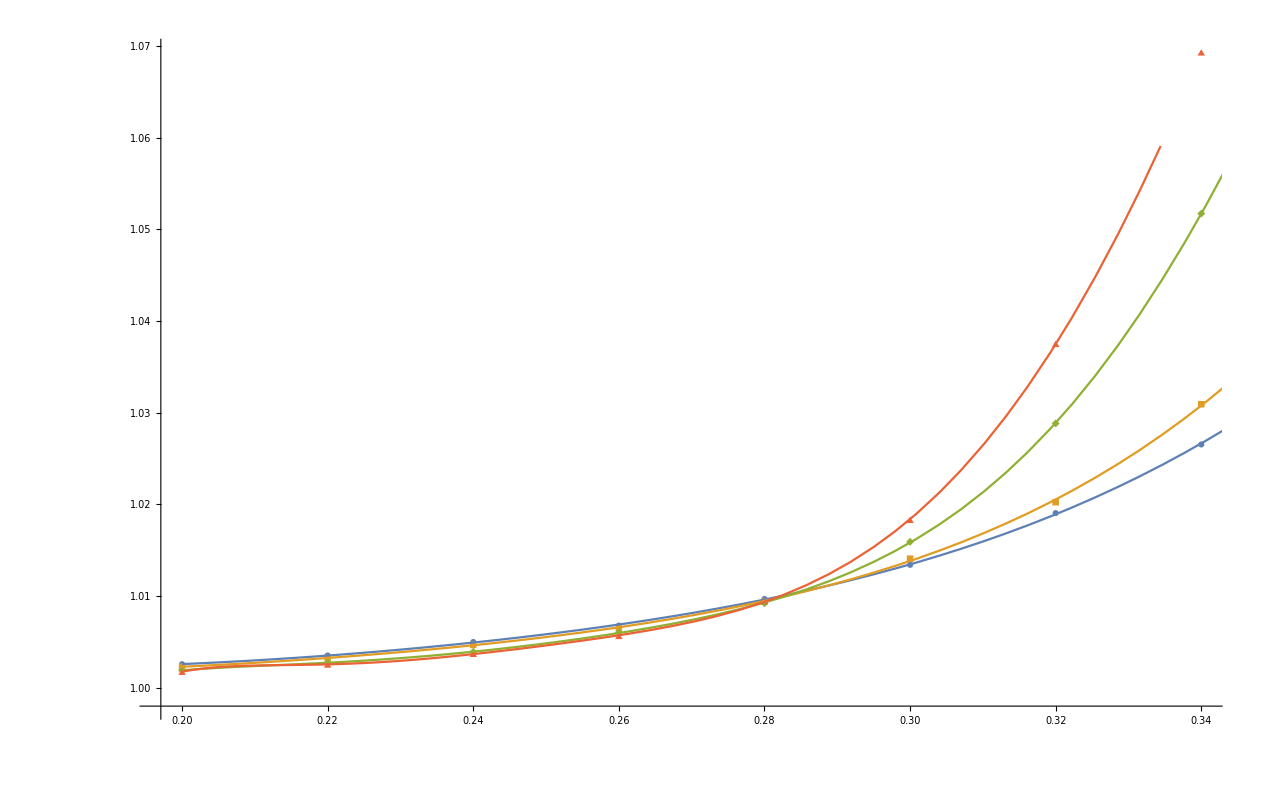

```mathematica
Show[ListPlot[{Y2[[4;;11]],Y3[[4;;11]],Y4[[4;;11]],Y5[[4;;11]]},PlotMarkers->Automatic],Plot[{f2[x],f3[x],f4[x],f5[x]},{x,0.2,0.35}]]
```

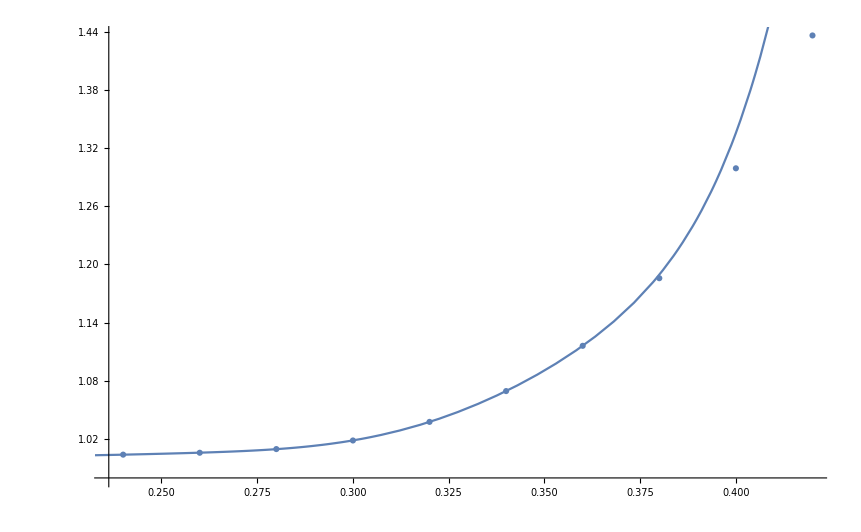

```mathematica
Show[ListPlot[{Y5[[6;;15]]},PlotMarkers->Automatic],Plot[{f5[x]},{x,0.2,0.45}]]
```

```mathematica
Show[ListPlot[{Y1,Y2,Y3,Y4,Y5},PlotMarkers->Automatic],Plot[{f1[x],f2[x],f3[x],f4[x],f5[x]},{x,0.20,0.45}]]
```

-Graphics-

#### Minimizing the χ using Monte Carlo algoritim.

```mathematica
Clear[f1,f2,f3,f4,f5];
Clear[Y1,Y2,Y3,Y4,Y5];
```

```mathematica
NL=5;
maxxW=100;
Af=1;
Af1 = 1;
yf=1;
Af2=1;
χf={1,0.5};
```

```mathematica
χ={};

For[i=1,i<500,i++,

A0=RandomReal[{-2,2}];
A1=RandomReal[{-2,2}];
(*A2=RandomReal[{-2,2}];*)
y=RandomReal[{-2,2}]; 

Y1 =MapAt[#-A0/100^y-A1/100^(2y)&,Select[α1,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y2 =MapAt[#-A0/500^y -A1/500^(2y)&,Select[α2,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y3 =MapAt[#-A0/1000^y -A1/1000^(2y)&,Select[α3,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y4 =MapAt[#-A0/5000^y-A1/1000^(2y) &,Select[α4,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y5 =MapAt[#-A0/10000^y -A1/1000^(2y)&,Select[α5,#[[1]]==sig &][[All,{2,3}]],{All,2}];

fit1=FindFit[Y1[[4;;12]],a + b x + c x^2 +dd x^3,{a,b,c,dd},x];
f1[x_]= a +b x + c x^2 + dd x^3/.fit1;
fit2=FindFit[Y2[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 ,{a,b,c,dd, e},x];
f2[x_]= a +b x + c x^2 + dd x^3+ e x^4 /.fit2;
fit3=FindFit[Y3[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5,{a,b,c,dd, e,f},x];
f3[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5/.fit3;
fit4=FindFit[Y4[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5+g x^6,{a,b,c,dd, e,f,g,h},x];
f4[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5+g x^6/.fit4;
fit5=FindFit[Y5[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5+g x^6+h x^7,{a,b,c,dd, e,f,g,h,k},x];
f5[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5+g x^6+h x^7/.fit5;

fall[x_]:={f1[x],f2[x],f3[x],f4[x],f5[x]};

WI={};
Do[
If[ii≠ jj,sol=FindRoot[fall[x][[ii]]-fall[x][[jj]]==0.,{x,0.35}];
AppendTo[WI,x/.sol]];
,{ii,1,NL},{jj,ii,NL}];
(*Wim=Mean[WI];*)
χ={};
Do[
Wc=RandomReal[{0.2,0.4}];
AppendTo[χ,{Wc,Sum[(WI[[i]]-Wc)^2,{i,1,Binomial[NL,2]}]}];
,{iW,1,maxxW}];

χm =Sort[χ,#1[[2]]<#2[[2]]&][[1]];

(* If[Dimensions[χf]=={0},χf=χm]; *)
(* χf = Sort[{χf,χm},#1[[2]]<#2[[2]]&][[1]]; *)

If[χm[[2]]<χf[[2]],χf=χm; Af=A0;Af1=A1; yf=y;]

]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
χm
```

{0.393798,17280.7}

```mathematica
χf
```

{0.281691,0.0000306261}

```mathematica
Af
```

0.411154

```mathematica
Af1
```

1.79628

```mathematica
A1
```

1.5674

```mathematica
Af2
```

1

```mathematica
yf
```

1.32795

```mathematica
Clear[{fit1,fit2,fit3,fit4,fit5}]
```

Clear::ssym: {fit1,fit2,fit3,fit4,fit5} is not a symbol or a string.

```mathematica
Yf1 =MapAt[#-Af/100^yf-Af1/100^(2 yf)&,Select[α1,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Yf2 =MapAt[#-Af/500^yf -Af1/500^(2 yf) &,Select[α2,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Yf3 =MapAt[#-Af/1000^yf-Af1/1000^(2 yf) &,Select[α3,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Yf4 =MapAt[#-Af/5000^yf-Af1/5000^(2 yf) &,Select[α4,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Yf5 =MapAt[#-Af/10000^yf-Af1/10000^(2 yf) &,Select[α5,#[[1]]==sig &][[All,{2,3}]],{All,2}];

fit1=FindFit[Yf1[[4;;12]],a + b x + c x^2 +dd x^3,{a,b,c,dd},x];
ff1[x_]= a +b x + c x^2 + dd x^3/.fit1;
fit2=FindFit[Yf2[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 ,{a,b,c,dd, e},x];
ff2[x_]= a +b x + c x^2 + dd x^3+ e x^4 /.fit2;
fit3=FindFit[Yf3[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5,{a,b,c,dd, e,f},x];
ff3[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5/.fit3;
fit4=FindFit[Yf4[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5+g x^6,{a,b,c,dd, e,f,g,h},x];
ff4[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5+g x^6/.fit4;
fit5=FindFit[Yf5[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5+g x^6+h x^7,{a,b,c,dd, e,f,g,h,k},x];
ff5[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5+g x^6+h x^7/.fit5;
```

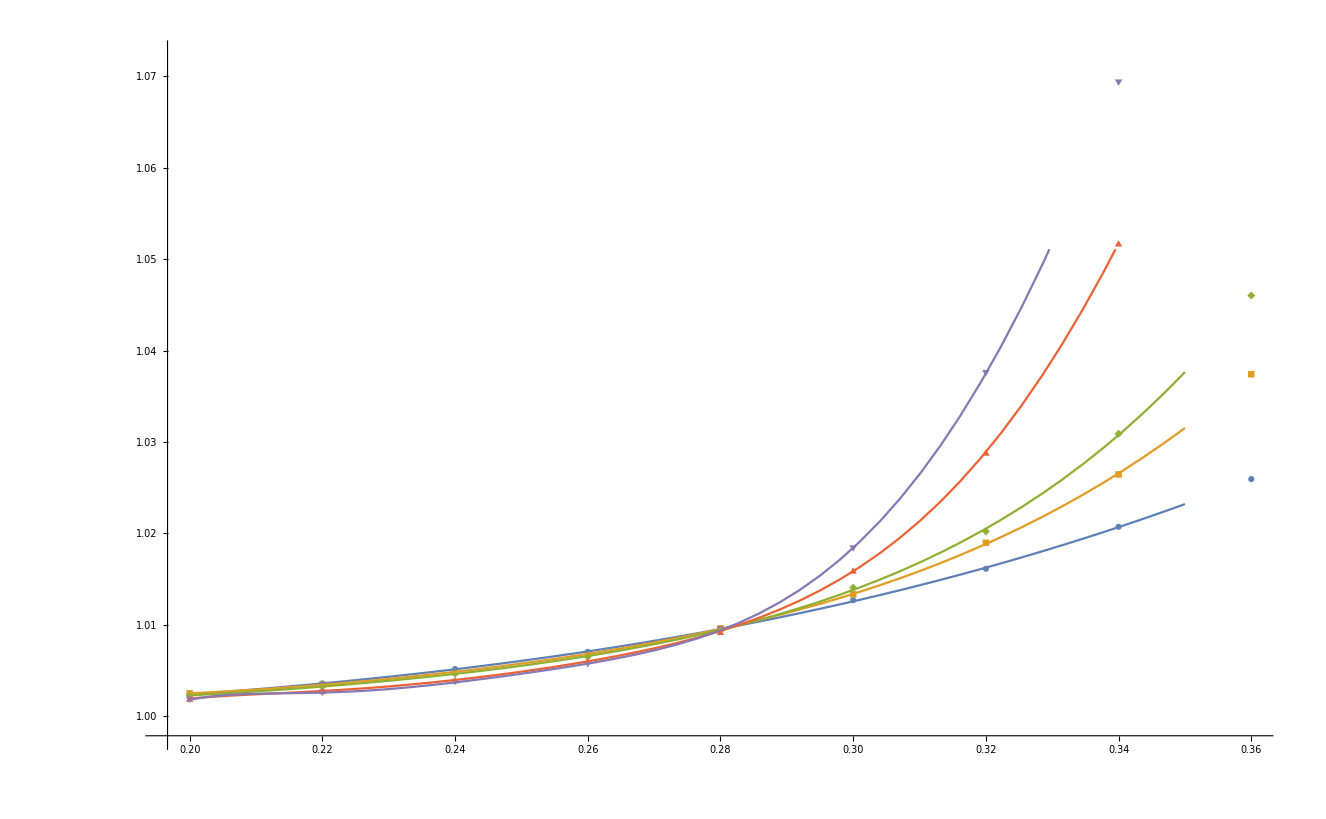

```mathematica
Show[ListPlot[{Yf1[[4;;12]],Yf2[[4;;12]],Yf3[[4;;12]],Yf4[[4;;12]],Yf5[[4;;12]]},PlotMarkers->Automatic],Plot[{ff1[x],ff2[x],ff3[x],ff4[x],ff5[x]},{x,0.2,0.35}]]
```

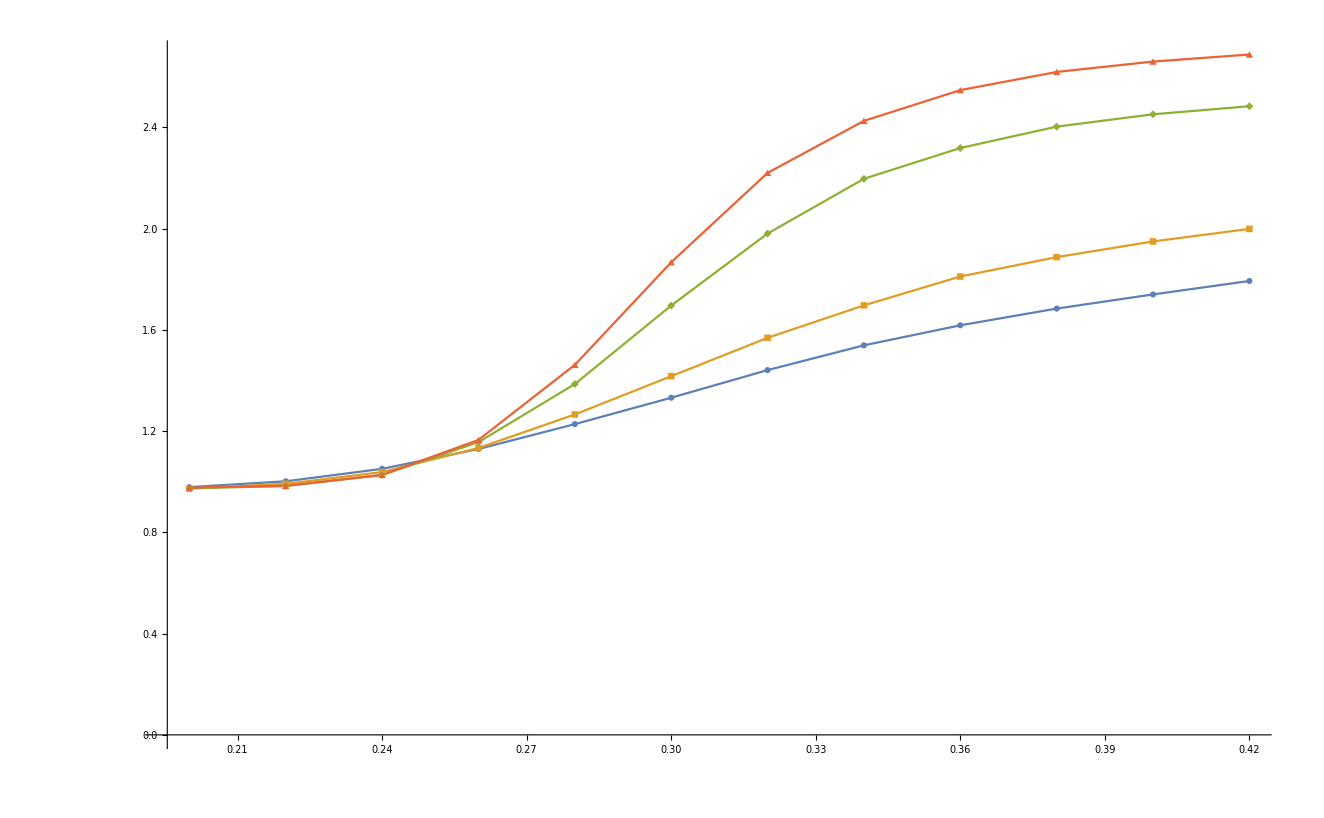

```mathematica
ListLinePlot[{(*Yf1[[4;;15]],*)Yf2[[4;;15]],Yf3[[4;;15]],Yf4[[4;;15]],Yf5[[4;;15]]},PlotMarkers->Automatic]
```

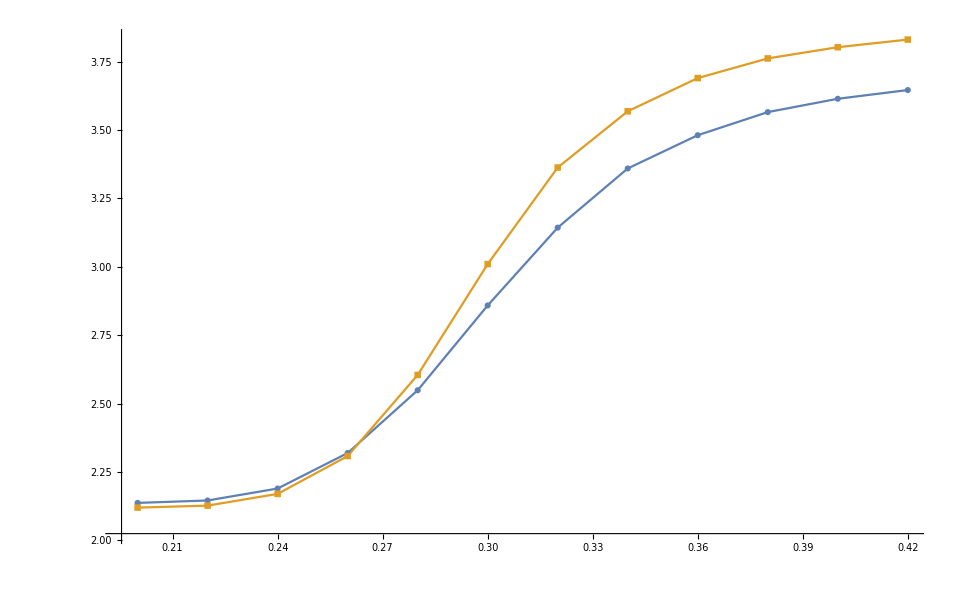

```mathematica
ListLinePlot[{(*Yf1[[4;;15]],Yf2[[4;;15]],Yf3[[4;;15]],*)Yf4[[4;;15]],Yf5[[4;;15]]},PlotMarkers->Automatic]
```

#### Fitting by steps

```mathematica
d0=0;
A00=0.0;
y0=0.0;
maxx=20;
W0=0.28;
stepW=0.12;
maxxW=200;
NL=5;
χall={};
imin=1;
min=0.25;
max=0.4;
stepd=0.4;
stepA=2.;
stepy=2.;
```

```mathematica
Clear[f1,f2,f3,f4,f5];
Clear[Y1,Y2,Y3,Y4,Y5]
```

```mathematica
results={};
χ={};
χall={};
χfinal={};
χplot={};
Do[
d=d0;(*+stepd(id -1)/maxx;*)
A0=A00+2*stepA(iA-1)/maxx;
y=y0+2*stepy(iy-1)/maxx;

Y1 =MapAt[#-A0/100^y &,Select[α1,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y2 =MapAt[#-A0/500^y &,Select[α2,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y3 =MapAt[#-A0/1000^y &,Select[α3,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y4 =MapAt[#-A0/5000^y &,Select[α4,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y5 =MapAt[#-A0/10000^y &,Select[α5,#[[1]]==sig &][[All,{2,3}]],{All,2}];

(*fit1=FindFit[Y1,a + b x+ c x^2,{a,b,c},x];
f1[x_]=a +b x + c x^2/.fit1;
fit2=FindFit[Y2,a + b x+ c x^2,{a,b,c},x];
f2[x_]=a +b x + c x^2 /.fit2;
fit3=FindFit[Y3,a + b x+ c x^2,{a,b,c},x];
f3[x_]=a +b x + c x^2 /.fit3;
fit4=FindFit[Y4,a + b x+ c x^2,{a,b,c},x];
f4[x_]=a +b x + c x^2 /.fit4;
fit5=FindFit[Y5,a + b x+ c x^2,{a,b,c},x];
f5[x_]=a +b x + c x^2/.fit5;*)

fit1=FindFit[Y1[[4;;12]],a + b x + c x^2 +dd x^3,{a,b,c,dd},x];
f1[x_]= a +b x + c x^2 + dd x^3/.fit1;
fit2=FindFit[Y2[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 ,{a,b,c,dd, e},x];
f2[x_]= a +b x + c x^2 + dd x^3+ e x^4 /.fit2;
fit3=FindFit[Y3[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5,{a,b,c,dd, e,f},x];
f3[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5/.fit3;
fit4=FindFit[Y4[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5+g x^6,{a,b,c,dd, e,f,g,h},x];
f4[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5+g x^6/.fit4;
fit5=FindFit[Y5[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5+g x^6+h x^7,{a,b,c,dd, e,f,g,h,k},x];
f5[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5+g x^6+h x^7/.fit5;

fall[x_]:={f1[x],f2[x],f3[x],f4[x],f5[x]};

WI={};
Do[
sol=FindRoot[fall[x][[ii]]-fall[x][[jj]]==0.,{x,0.3}];
If[ii≠ jj,AppendTo[WI,x/.sol]];
,{ii,1,NL},{jj,ii+1,NL}];
χ={};
WIm=Mean[WI];
Do[
(*Wc=W0+stepW(iW-1)/maxxW;*)
AppendTo[χ,{Wc,Sum[(WI[[i]]-WIm)^2,{i,1,Binomial[NL,2]}]}];
AppendTo[χall,{Wc,Sum[(WI[[i]]-WIm)^2,{i,1,Binomial[NL,2]}]}];
,{iW,1,maxxW}];
χfinal=Sort[χ,#1[[2]]<#2[[2]]&];
AppendTo[results,{χfinal[[1]][[2]],χfinal[[1]][[1]],A0,d,y}];
AppendTo[χplot,{A0,y,χfinal[[1]][[2]]}];
,(*{id,1,maxx},*){iA,1,maxx},{iy,1,maxx}];
χallfinal=Sort[χall,#1[[2]]<#2[[2]]&];
χallfinal[[1]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{0.263284,0.0000393966}

```mathematica
χallfinal[[1]]
```

{0.263284,0.0000393966}

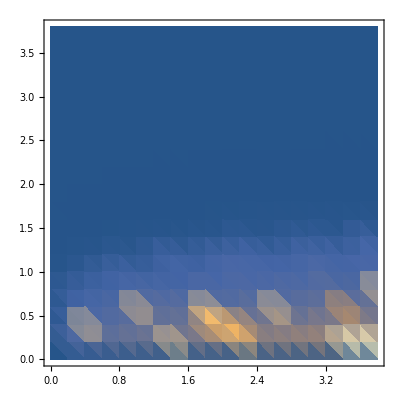

```mathematica
ListDensityPlot[χplot,PlotRange->All]
```

```mathematica
resultsfinal=Sort[results,#1[[1]]<#2[[1]]&];
```

```mathematica
resultsfinal[[1]]
```

{0.0000393966,0.263284,0.2,0,1.2}

```mathematica
d=resultsfinal[[1]][[4]];
A0= resultsfinal[[1]][[3]];
y=resultsfinal[[1]][[5]];
Wc=resultsfinal[[1]][[2]];

(*Y1 =MapAt[#-A0/100^y &,Select[α1,#[[1]]==sig &][[All,{2,3}]],{All,2}];*)
Y2 =MapAt[#-A0/500^y &,Select[α2,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y3 =MapAt[#-A0/1000^y &,Select[α3,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y4 =MapAt[#-A0/5000^y &,Select[α4,#[[1]]==sig &][[All,{2,3}]],{All,2}];
Y5 =MapAt[#-A0/10000^y &,Select[α5,#[[1]]==sig &][[All,{2,3}]],{All,2}];

(*fit1=FindFit[Y1,a + b x+ c x^2,{a,b,c},x];
f1[x_]=a +b x + c x^2/.fit1;*)
(*fit2=FindFit[Y2,a + b x+ c x^2,{a,b,c},x];
f2[x_]=a +b x + c x^2 /.fit2;
fit3=FindFit[Y3,a + b x+ c x^2,{a,b,c},x];
f3[x_]=a +b x + c x^2/.fit3;
fit4=FindFit[Y4,a + b x+ c x^2,{a,b,c},x];
f4[x_]=a +b x + c x^2 /.fit4;
fit5=FindFit[Y5,a + b x+ c x^2,{a,b,c},x];
f5[x_]=a +b x + c x^2 /.fit5;*)

fit1=FindFit[Y1[[4;;12]],a + b x + c x^2 +dd x^3,{a,b,c,dd},x];
f1[x_]= a +b x + c x^2 + dd x^3/.fit1;
fit2=FindFit[Y2[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 ,{a,b,c,dd, e},x];
f2[x_]= a +b x + c x^2 + dd x^3+ e x^4 /.fit2;
fit3=FindFit[Y3[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5,{a,b,c,dd, e,f},x];
f3[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5/.fit3;
fit4=FindFit[Y4[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5+g x^6,{a,b,c,dd, e,f,g,h},x];
f4[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5+g x^6/.fit4;
fit5=FindFit[Y5[[4;;12]],a + b x + c x^2 +dd x^3+ e x^4 + f x^5+g x^6+h x^7,{a,b,c,dd, e,f,g,h,k},x];
f5[x_]= a +b x + c x^2 + dd x^3+ e x^4 + f x^5+g x^6+h x^7/.fit5;
```

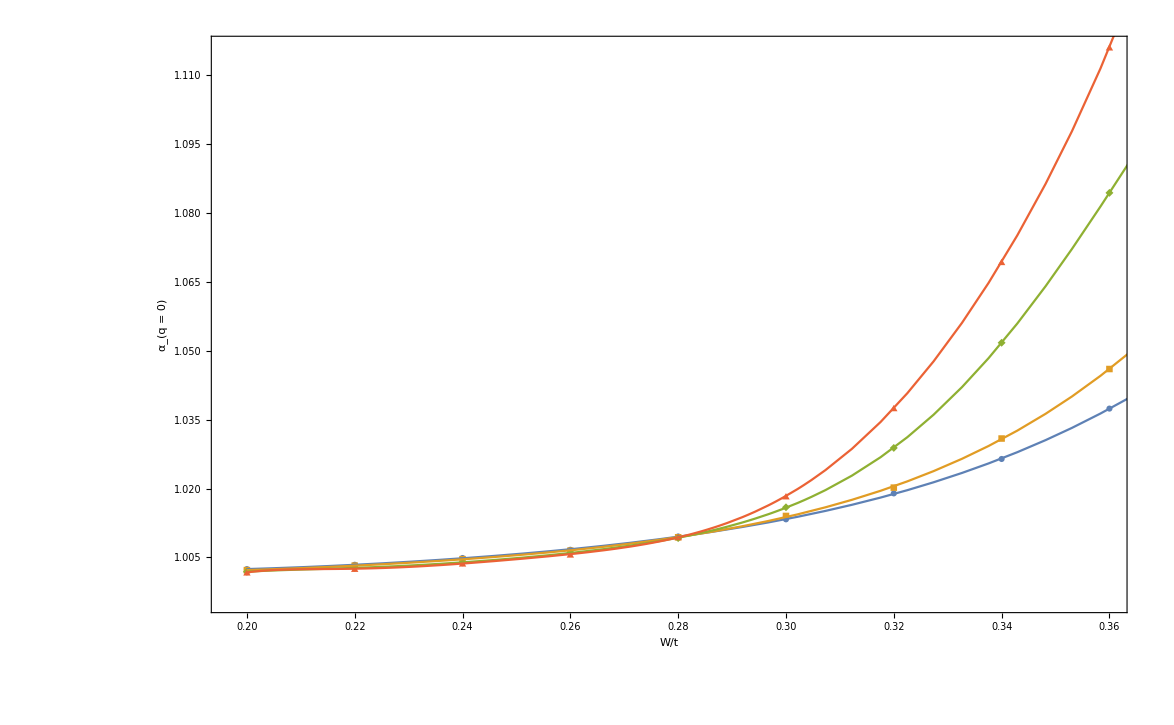

```mathematica
Show[ListPlot[{Y2[[4;;12]],Y3[[4;;12]],Y4[[4;;12]],Y5[[4;;12]]},Frame-> True,FrameLabel->{"W/t","α_(q = 0)"}(*,PlotRange->All*),PlotMarkers->Automatic],Plot[{f2[x],f3[x],f4[x],f5[x]},{x,0.2,0.45},PlotRange-> All]]
```